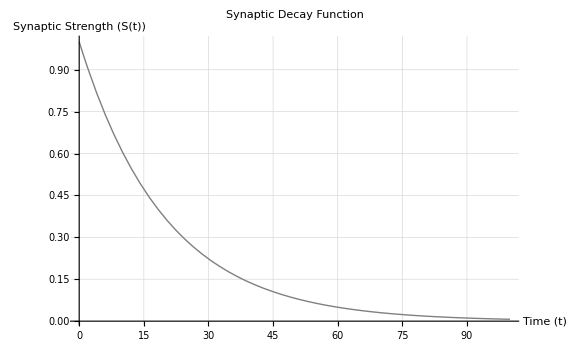

```mathematica
(* Define the parameters *)
S0=1;
tau=20;

(* Define the synaptic decay function *)
SynapticDecay[t_]:=S0*Exp[-t/tau]

(* Plot the synaptic decay function in grayscale *)
Plot[SynapticDecay[t],{t,0,100},
 PlotLabel->"Synaptic Decay Function",
 AxesLabel->{"Time (t)","Synaptic Strength (S(t))"},
 PlotStyle->{GrayLevel[0.5],Thick},(* Use GrayLevel for grayscale *)
 GridLines->Automatic,
 PlotRange->All,
 ImageSize->Large]
```

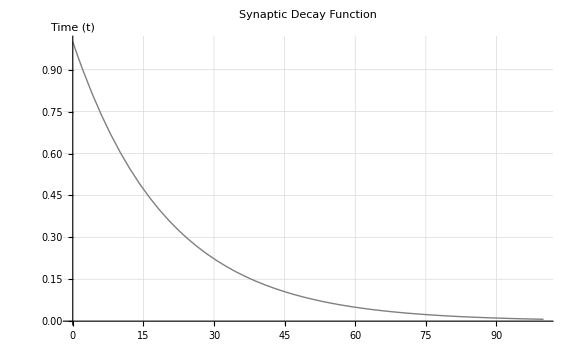

```mathematica
(* Define the parameters *)
S0=1;
tau=20;

(* Define the synaptic decay function *)
SynapticDecay[t_]:=S0*Exp[-t/tau]

(* Plot the synaptic decay function in grayscale *)
Plot[SynapticDecay[t],{t,0,100},
 PlotLabel->Style["Synaptic Decay Function",FontSize->16],
 AxesLabel->Style["Time (t)","Synaptic Strength (S(t))",FontSize->16],
 PlotStyle->{GrayLevel[0.5],Thick},(* Use GrayLevel for grayscale *)
 GridLines->Automatic,
 PlotRange->All,
 ImageSize->Large]
```